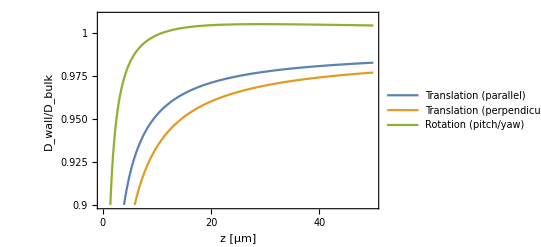

```mathematica
(* Bitter, Yang, Duncan Fairbrother, Bevan 2017 *)
d = 0.5 μm; (* helical diameter *)
L = 6 μm; a = d/2; p = L/(2a);
z = Range[0,50,0.1] μm; (* distance from the wall *)
Subscript[T, par]=(0.9909(z/a)^3+0.3907(z/a)^2-0.1832(z/a)-0.001815)/((z/a)^3+2.03(z/a)^2-0.3874(z/a)-0.07533);
Subscript[T, perp]=(0.9888(z/a)^3+0.788(z/a)^2-0.207(z/a)-0.004766)/((z/a)^3+3.195(z/a)^2-0.09612(z/a)-0.1523);
Subscript[R, perp]=(0.998(z/a)^3+131.1(z/a)^2+21.25(z/a)+0.01275)/((z/a)^3+128.7(z/a)^2+121.1(z/a)+2.897);

ListLinePlot[{Transpose@{z/μm,Subscript[T, par]},
Transpose@{z/μm,Subscript[T, perp]},
Transpose@{z/μm,Subscript[R, perp]}},
Frame->True, 
FrameLabel->{"z [μm]","D_wall/D_bulk"},FrameTicks->{{{0.90,0.925,{0.95,"0.950"},0.975,1},None},{{0,10,20,30,40,50},None}},
RotateLabel->False,
PlotLegends->{"Translation (parallel)",
"Translation (perpendicular)", "Rotation (pitch/yaw)"},
(* Epilog->{Directive[Gray,Dashed],Line[{{15,0},{15,1.01}}],Line[{{30,0},{30,1.01}}]}, *)
PlotRange->{{0,50},{0.9,1.01}}
]
```

```mathematica
15000/500
```

30

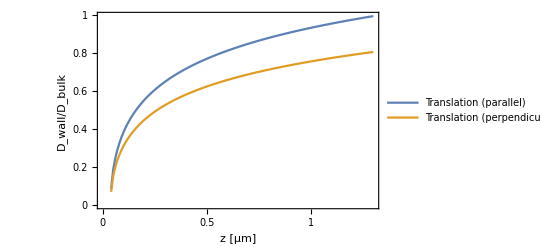

```mathematica
(* Hunt, Gittes, Howard 1994 *)
d = 0.075 μm; (* helical diameter *)
a = d/2; L = 6 μm;
h = Range[0.01,1.3,0.01] μm; (* distance from the wall *)
Subscript[RD, par]=ArcCosh[h/a]/(Log[L/(2a)]-0.114);
Subscript[RD, perp]=ArcCosh[h/a]/(Log[L/(2a)]+0.886);
ListLinePlot[{Transpose@{h/μm,Subscript[RD, par]},
Transpose@{h/μm,Subscript[RD, perp]}},
Frame->True, 
FrameLabel->{"z [μm]","D_wall/D_bulk"},
FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},None},
{{0,0.25,0.5,0.75,1,1.25},None}}, 
RotateLabel->False,
(* PlotRange->{{0,50},{0.9,1.01}}, *)
PlotLegends->{"Translation (parallel)",
"Translation (perpendicular)", "Rotation (pitch/yaw)"}
(* Epilog->{Directive[Gray,Dashed],Line[{{15,0},{15,1.01}}],Line[{{30,0},{30,1.01}}]}, *)
]
```